## Code to detect if inside polygon by Shreyas & Arifa, Jan 20, 2019

### Becker fix : AppendTo[points, First[points]]; rather than points = AppendTo[points, First[points]];, Made temp variable pointsIn

InitializationObjects

```mathematica
pointinregionREV1[points_,{x_,y_}]:=Module[{a,b,c},
(*a = Δy, b = Δx, *)
a=Table[points⟦i,2⟧-points⟦i+1,2⟧,{i,1,Length[points]-1,1}];
b=Table[points⟦i+1,1⟧-points⟦i,1⟧,{i,1,Length[points]-1,1}];
c=Table[(points⟦i,1⟧*points⟦i+1,2⟧)-(points⟦i+1,1⟧*points⟦i,2⟧),{i,1,Length[points]-1,1}];
(*         For all, is it true that  (     ax + by + c ≤ 0 )*)
And@@((#>0)&/@Chop[((#*x)&/@a)+((#*y)&/@b)+(#&/@c)])
]
```

```mathematica
pointinregionREV2[pointsIn_,{x_,y_}]:=Module[{points},
(*a = Δy, b = Δx, *)
points = Append[pointsIn,First[pointsIn]];
And@@Table[((x*(points⟦i,2⟧-points⟦i+1,2⟧)) +( y*(points⟦i+1,1⟧-points⟦i,1⟧) )+  (points⟦i,1⟧*points⟦i+1,2⟧)-(points⟦i+1,1⟧*points⟦i,2⟧))>0,{i,1,Length[points]-1,1}]
]

pointinregionREV3[poly_,{x_,y_}]:=(*Module[{}, *)(*Assumes edge repeats the first vertex at the end*)
(*a = Δy, b = Δx, *)
(*And@@Table[((x*(points⟦i,2⟧-points⟦i+1,2⟧)) +( y*(points⟦i+1,1⟧-points⟦i,1⟧) )+  (points⟦i,1⟧*points⟦i+1,2⟧)-(points⟦i+1,1⟧*points⟦i,2⟧))>0,{i,1,Length[points]-1,1}]*)
(*And@@*)And@@((#<0)&/@(x(#⟦;;,2⟧-RotateRight[#]⟦;;,2⟧) +  y(RotateRight[#]⟦;;,1⟧-#⟦;;,1⟧) +  #⟦;;,1⟧RotateRight[#]⟦;;,2⟧-RotateRight[#]⟦;;,1⟧#⟦;;,2⟧&@poly))

(*pointinregionREV4[poly_,{x_,y_}]:=(*Module[{}, *)(*Assumes edge repeats the first vertex at the end*)
(*a = Δy, b = Δx, *)
And@@((#<0)&/@(({(#⟦;;,2⟧-RotateRight[#]⟦;;,2⟧)  ,(RotateRight[#]⟦;;,1⟧-#⟦;;,1⟧) ,  (#⟦;;,1⟧RotateRight[#]⟦;;,2⟧-RotateRight[#]⟦;;,1⟧#⟦;;,2⟧)}&@poly).{x,y,1}))*)
```

```mathematica
(*winding[] and testpoint[] from https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon *)
winding[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]
(*true if pt  is inside polygon*)
testpoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0
```

### Assignment: which is faster? Your point_in_region, or the winding calculation Using Timing. Generate a polygon Generate 10,000 random points Evaluate each point if it is in or out Compare

Speed Test

```mathematica
convexShape = {{2+(√3)/2,1/2},{2,2},{2-(√3)/2,1/2}}
(*pointinregionREV3[convexShapeE,{0,0}]*)
pointinregionREV1[convexShapeE,{0,0}]
```

{{2+(√3)/2,1/2},{2,2},{2-(√3)/2,1/2}}

True

```mathematica
{{2+(√3)/2,1/2},{2,2},{2-(√3)/2,1/2}}
```

{{2+(√3)/2,1/2},{2,2},{2-(√3)/2,1/2}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{23,977},{23,977},{23,977}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{34,966},{34,966},{34,966}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{39,961},{39,961},{39,961}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{47,953},{47,953},{47,953}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{46,954},{46,954},{46,954}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{49,951},{49,951},{49,951}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{52,948},{52,948},{52,948}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{51,949},{51,949},{51,949}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{52,948},{52,948},{52,948}}

{TRUE,FALSE}->{TestPoint, Book1, Book2}->{{51,949},{51,949},{51,949}}

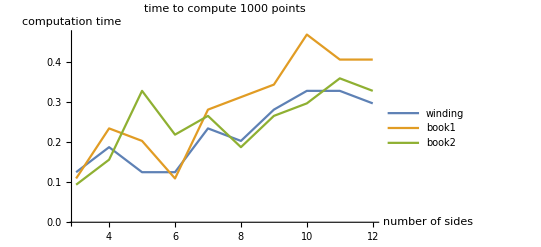

```mathematica
(*Module[{g,o,bound,pts,time3Tests,result1,result2,result3},g=0;*)
o={2,1};
(*n=3;(*"Number of sides"*)*)
bound=5CirclePoints[4];
pts = RandomPoint[Polygon[bound],1000];
time3Tests = Table[
convexShape=(o+ #)&/@CirclePoints[n];
result1=Timing[testpoint[convexShape,#]&/@pts];
result2=Timing[pointinregionREV2[convexShape,#]&/@pts];
result3=Timing[pointinregionREV3[convexShape,#]&/@pts];
Print["{TRUE,FALSE}->{TestPoint, Book1, Book2}->",{{Length@Cases[result1⟦2⟧,True],Length@Cases[result1⟦2⟧,False]},{Length@Cases[result2⟦2⟧,True],Length@Cases[result2⟦2⟧,False]},
{Length@Cases[result3⟦2⟧,True],Length@Cases[result3⟦2⟧,False]}}];
{First[result1],First[result2],First[result3]},{n,3,12}];

ListLinePlot[Transpose@time3Tests,DataRange->{3,12},PlotLegends->{"winding","book1","book2"},AxesLabel->{"number of sides","computation time"},PlotLabel->"time to compute 1000 points"](*]*)
```

Winding Method Time = 0.046875

Book Method1 Time =0.046875

Book Method2 Time =0.046875

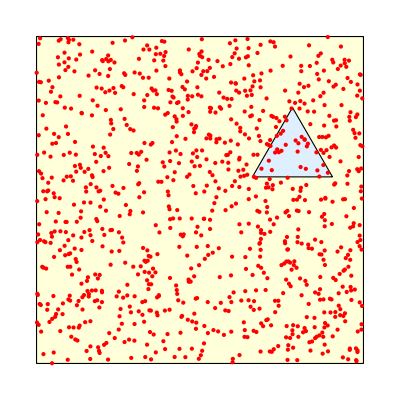

```mathematica
g=0;
o={2,1};
n=3;(*"Number of sides"*)
oldr={0,0};
bound=5CirclePoints[4];
convexShape=(o+ #)&/@CirclePoints[n];
pts = RandomPoint[Polygon[bound],1000];
result1=Timing[testpoint[convexShape,#]&/@pts];
result2=Timing[pointinregionREV2[convexShape,#]&/@pts];
convexShapeE = Append[convexShape,First[convexShape]];
result3=Timing[pointinregionREV3[convexShapeE,#]&/@pts];
Print[StringForm["Winding Method Time = ``",result1⟦1⟧]];
Print[StringForm["Book Method1 Time =``",result2⟦1⟧]];
Print[StringForm["Book Method2 Time =``",result3⟦1⟧]];
(*Print[r];*)
Graphics[
{EdgeForm[Thin]
,{LightYellow
,Polygon[bound]}
,{LightBlue
,Polygon[convexShape]},
{Red,Point[pts]}
(*If[pointinregionREV2[points,r]
,{Red,Point[r]},{Green,Point[r]}]*)
}
]
```

Demo code

```mathematica
Manipulate[Module[{g,oldr,bound,convexShape,pts,points,result1,result2},
(*Module[{bound,convexShape},*)
g=0;
oldr={0,0};
bound=5CirclePoints[4];
convexShape=(o+ #)&/@CirclePoints[n];
pts = RandomPoint[Polygon[bound],1000];
result1=Timing[testpoint[convexShape,#]&/@pts];
result2=Timing[pointinregionREV2[convexShape,#]&/@pts];
(*Print[r];*)
Graphics[
{EdgeForm[Thin]
,{LightYellow
,Polygon[bound]}
,{LightBlue
,Polygon[convexShape]},
{Red,Point[pts]}
(*If[pointinregionREV2[points,r]
,{Red,Point[r]},{Green,Point[r]}]*)
,Blue,
Text[StringForm["Winding Method Time=``",result1⟦1⟧],{0,4}],
Text[StringForm["Book Method Time   =``",result2⟦1⟧],{0,3.75}]
}
]](*]*)
,{{n,3,"Number of sides"},3,9,1}
(*,{{r,{-2,2}},{-5/(√2),-5/(√2)},{5/(√2),5/(√2)},Locator}*)
,{{o,{2,1}},{-5/(√2),-5/(√2)},{5/(√2),5/(√2)},Locator}
]
```

```mathematica
convexShape=CirclePoints[7]
points=AppendTo[convexShape,convexShape⟦1⟧]
```

{{Sin[π/7],-Cos[π/7]},{Cos[π/14],-Sin[π/14]},{Cos[(3 π)/14],Sin[(3 π)/14]},{0,1},{-Cos[(3 π)/14],Sin[(3 π)/14]},{-Cos[π/14],-Sin[π/14]},{-Sin[π/7],-Cos[π/7]}}

{{Sin[π/7],-Cos[π/7]},{Cos[π/14],-Sin[π/14]},{Cos[(3 π)/14],Sin[(3 π)/14]},{0,1},{-Cos[(3 π)/14],Sin[(3 π)/14]},{-Cos[π/14],-Sin[π/14]},{-Sin[π/7],-Cos[π/7]},{Sin[π/7],-Cos[π/7]}}